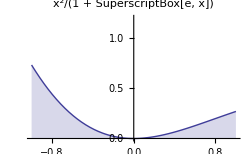

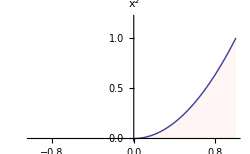

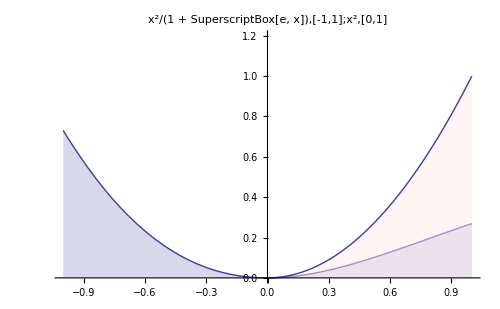

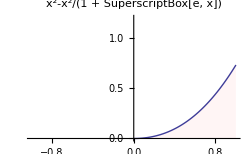

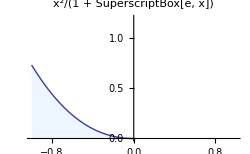

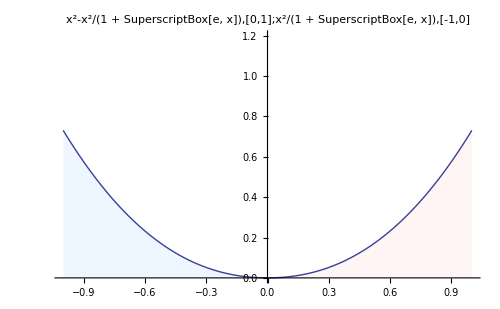

```mathematica
plt1=Plot[x^2/(1+Exp[x]),{x,-1,1},Filling->Axis,PlotRange->{{-1,1},{0,1.2}},PlotLabel->"x^2/(1 + SuperscriptBox[e, x])",ImageSize->250]
plt2=Plot[x^2,{x,0,1},Filling->Axis,FillingStyle->Directive[Opacity[0.5],LightPink],PlotRange->{{-1,1},{0,1.2}},PlotLabel->"x^2",ImageSize->250]
plt12=Show[plt1,plt2,PlotLabel->"x^2/(1 + SuperscriptBox[e, x]),[-1,1];x^2,[0,1]",ImageSize->500]
plt3=Plot[x^2-x^2/(1+Exp[x]),{x,0,1},Filling->Axis,FillingStyle->Directive[Opacity[0.5],LightPink],PlotRange->{{-1,1},{0,1.2}},PlotLabel->"x^2-x^2/(1 + SuperscriptBox[e, x])",ImageSize->250]
plt4=Plot[x^2/(1+Exp[x]),{x,-1,0},Filling->Axis,FillingStyle->Directive[Opacity[0.5],LightBlue],PlotRange->{{-1,1},{0,1.2}},PlotLabel->"x^2/(1 + SuperscriptBox[e, x])",ImageSize->250]
plt34=Show[plt3,plt4,PlotLabel->"x^2-x^2/(1 + SuperscriptBox[e, x]),[0,1];x^2/(1 + SuperscriptBox[e, x]),[-1,0]",ImageSize->500]
```

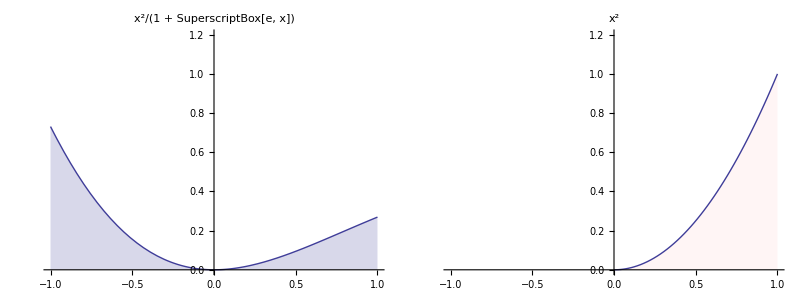
-Graphics-
-Graphics-

~/Desktop/1.png

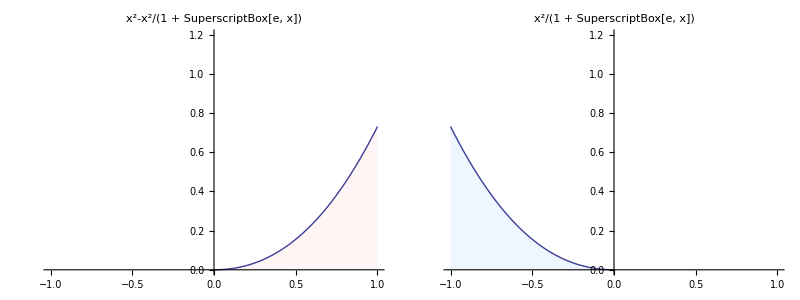
-Graphics-
-Graphics-

~/Desktop/2.png

```mathematica
Grid[{{Grid[{{plt1,plt2}}]},{plt12}}]
Export["~/Desktop/1.png",%]
Grid[{{Grid[{{plt3,plt4}}]},{plt34}}]
Export["~/Desktop/2.png",%]
```